# 小波分析

令人意外的是，Mathematica提供了很好的小波分析的配套函数，通过官方给出的说明文档，可以让我们熟悉小波分析的操作流程。

在几天的思考中，大概对小波分析有如下的认识：

1. 将函数视作无穷维的向量，选取一组基函数作为基用来表示f(x)，这个用于拟合f(x)的级数就是基向量与系数向量的点积

	1. 系数向量由基函数的对偶函数与f(x)的点积求得，对偶函数的求法未知。但如果基函数是两两正交的，那么基函数与它的对偶函数一致
	2. 基函数的选取尽量是正交的，而且是紧支撑的

2. 假设选取了一组紧支撑的函数，那么函数非零值的宽度决定了“分辨率”，系数向量决定了强度。宽度小的函数所张成的空间必定包含宽度大的函数所张成的空间。这样的函数称为“尺度函数”。

3. 假设一个宽度小的函数（组）张成空间V1，另一个宽度大的函数（组）张成空间V2，则V2包含于V1，V1-V2的基函数（组）称为小波函数

4. 如果用尺度函数表示f(x)，则每次分辨率的增加都会使无穷级数整体发生变化，而如果用小波函数表示f(x)，则每次分辨率的增加就是在级数的末尾增加一个（组）尾项

比如以哈尔函数为基的话

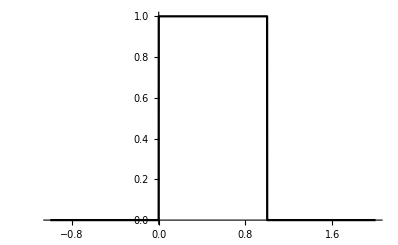

```mathematica
Plot[WaveletPhi[HaarWavelet[],x],{x,-1,2},Exclusions->None,PlotTheme->"Monochrome"]
```

它所给出的一个基函数组可以动态的表示为

```mathematica
Animate[Plot[√(2^j)WaveletPhi[HaarWavelet[],2^j x-k],{x,-1,3},Exclusions->None,PlotTheme->"Monochrome",PlotRange->{{-1,3},{-0.5,2}}],{j,0,2},{k,0,1},AnimationRunning->False]
```

下面通过Mathematica给出lena图的小波变换结果，这里进行三阶小波变换。首先需要默认文件路径进行修改

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

F:\MyCode\笔记\数字图像处理

```mathematica
pic =Import["lena.jpg"]
```

-Graphics-

```mathematica
dwd=DiscreteWaveletTransform[pic,Automatic,3]
```

DiscreteWaveletData[<<DWT>>, <3>, {204, 204}]

```mathematica
WaveletImagePlot[dwd]
```

-Graphics-